### BFO R71 DW FEM

```mathematica
Clear["Global`*"];
$HistoryLength=0;
```

```mathematica
Needs["VariationalMethods`"];
Needs["NDSolve`FEM`"];
perturbationOP[eqn_,functions_,functions0_,dfunctions_,λ_]:=Module[{ϵ},Normal@Series[
eqn/.Thread[functions->Map[Function[{x,z},#]&,Through[functions0[x,z]]+λ ϵ Through[dfunctions[x,z]]]],{ϵ,0,1}]/.ϵ->1];
PDEtoMatrix[{pde_,Γ___},u_,r__]:=Module[{ndstate,feData,sd,bcData,methodData,pdeData},{ndstate}=NDSolve`ProcessEquations[Flatten[{pde,Γ}],u,Sequence@@{r}];
sd=ndstate["SolutionData"][[1]];
feData=ndstate["FiniteElementData"];
pdeData=feData["PDECoefficientData"];
bcData=feData["BoundaryConditionData"];
methodData=feData["FEMMethodData"];
{DiscretizePDE[pdeData,methodData,sd],DiscretizeBoundaryConditions[bcData,methodData,sd],sd,methodData}]
```

#### parameters and coefficients

```mathematica
paramsBFO={Subscript[Δ, 1]->4 10^-10,Subscript[Δ, 2]->4 10^-10,Subscript[Δ, 3]->4 10^-10,Subscript[α, 1]->8.78 10^5(T-830),Subscript[α, 11]->4.71 10^8,Subscript[α, 12]->5.74 10^8,Subscript[α, 111]->0,Subscript[α, 112]->0,Subscript[α, 123]->0,Subscript[G, 1111]->0.6 0.98 10^-10,Subscript[G, 1122]->0,Subscript[G, 1212]->0.6 0.98 10^-10,Subscript[C, 1111]-> 3.02 10^11,Subscript[C, 1122]-> 1.62 10^11,Subscript[C, 1212]-> 0.68 10^11,Subscript[Q, 1111]->0.035,Subscript[Q, 1122]->-0.0175 ,Subscript[Q, 1212]->0.02015,Subscript[F, 1111]->0.3 10^-10,Subscript[F, 1122]->-0.15 10^-10,Subscript[F, 1212]->0.2 10^-10,Subscript[f, 1111]->0,Subscript[f, 1122]->0,Subscript[f, 1212]->0}/.T->300;
paramsBFO={Subscript[Δ, 1]->5 10^-10,Subscript[Δ, 2]->4 10^-10,Subscript[Δ, 3]->4 10^-10,Subscript[α, 1]->8.78 10^5(T-830),Subscript[α, 11]->4.71 10^8,Subscript[α, 12]->5.74 10^8,Subscript[α, 111]->0,Subscript[α, 112]->0,Subscript[α, 123]->0,Subscript[G, 1111]->0.6 0.98 10^-10,Subscript[G, 1122]->0,Subscript[G, 1212]->0.6 0.98 10^-10,Subscript[C, 1111]-> 3.02 10^11,Subscript[C, 1122]-> 1.62 10^11,Subscript[C, 1212]-> 0.68 10^11,Subscript[Q, 1111]->0.035,Subscript[Q, 1122]->-0.0175 ,Subscript[Q, 1212]->0.02015,Subscript[F, 1111]->0.3 10^-10,Subscript[F, 1122]->-0.15 10^-10,Subscript[F, 1212]->0.2 10^-10,Subscript[f, 1111]->0,Subscript[f, 1122]->0,Subscript[f, 1212]->0}/.T->300;
Cijkl=Cijmn=Cklmn=SparseArray[{{i_,i_,i_,i_}->Subscript[C, 1111],{i_,i_,j_,j_}/;i≠j->Subscript[C, 1122],{i_,j_,i_,j_}/;i≠j->Subscript[C, 1212]},{3,3,3,3}];
sijkl=Array[Subscript[s, ##]&,{3,3,3,3}];
sijkl=sijmn=sijkl/.Solve[Normal[TensorContract[Cijkl⊗sijkl,{{3,5},{4,6}}]]==Table[KroneckerDelta[i,k]KroneckerDelta[j,l],{i,3},{j,3},{k,3},{l,3}],Flatten@sijkl][[1]];
Qmnkl=SparseArray[{{m_,m_,m_,m_}->Subscript[Q, 1111],{m_,m_,n_,n_}/;m≠n->Subscript[Q, 1122],{m_,n_,m_,n_}/;m≠n->Subscript[Q, 1212]},{3,3,3,3}];
(*qijkl=SparseArray[{{i_,i_,i_,i_}->Subscript[Q, 1111],{i_,i_,j_,j_}/;i≠j->Subscript[Q, 1122],{i_,j_,i_,j_}/;i≠j->Subscript[Q, 1212]},{3,3,3,3}];
qparams={Subscript[q, 1111]->2 Subscript[C, 1111] Subscript[Q, 1111]+4 Subscript[C, 1122] Subscript[Q, 1122],Subscript[q, 1122]->2 Subscript[C, 1122] Subscript[Q, 1111]+2 Subscript[C, 1111] Subscript[Q, 1122]+2 Subscript[C, 1122] Subscript[Q, 1122],Subscript[q, 1212]->2 Subscript[C, 1212] Subscript[Q, 1212]};*)
qijkl=TensorContract[2Cijmn⊗Qmnkl,{{3,5},{4,6}}];
Gijkl=SparseArray[{{i_,i_,i_,i_}->Subscript[G, 1111],{i_,i_,j_,j_}/;i≠j->Subscript[G, 1122],{i_,j_,i_,j_}/;i≠j->Subscript[G, 1212]},{3,3,3,3}];
Fijkl=fmnkl=SparseArray[{{i_,i_,i_,i_}->Subscript[F, 1111],{i_,i_,j_,j_}/;i≠j->Subscript[F, 1122],{i_,j_,i_,j_}/;i≠j->Subscript[F, 1212]},{3,3,3,3}];
(*fijkl=TensorContract[sijmn⊗Fmnkl,{{3,5},{4,6}}];*)
αi=SparseArray[{{i_}->Subscript[α, 1]},{3}];
αij=SparseArray[{{i_,i_}->2 Subscript[α, 11],{i_,j_}/;i≠j->Subscript[α, 12]},{3,3}];
αijk=SparseArray[{{i_,i_,i_}->2 Subscript[α, 111],{i_,i_,j_}/;i≠j->2/3 Subscript[α, 112],{i_,j_,i_}/;i≠j->2/3 Subscript[α, 112],{j_,i_,i_}/;i≠j->2/3 Subscript[α, 112],{i_,j_,k_}/;i≠j&&i≠k&&j≠k->1/3 Subscript[α, 123]},{3,3,3}];
```

#### Tensors

```mathematica
R={x,y,z};
OPs={Subscript[u, 1]@@R,Subscript[u, 2]@@R,Subscript[u, 3]@@R,Subscript[P, 1]@@R,Subscript[P, 2]@@R,Subscript[P, 3]@@R};
ndim=Length@R;
Subscript[r, i_]:=R[[i]];
Pk=Pl=Array[Subscript[P, #]@@R&,{3}];
Pi2=Pj2=Pk2=Array[(Subscript[P, #]@@R)^2&,{3}];
(Pij=Pkl=Pmn=Array[D[Subscript[P, #1]@@R,Subscript[r, #2]]&,{3,ndim}])//MatrixForm;
(ϵij=ϵkl=ϵmn=SparseArray[{{i_,j_}/;i==j->Subscript[ϵ, i,j]@@R,{i_,j_}/;i<j->Subscript[ϵ, i,j]@@R,{i_,j_}/;i>j->Subscript[ϵ, j,i]@@R},{3,3}])//MatrixForm;
(ϵijl=ϵmnl=SparseArray[{{i_,j_,k_}/;i==j:>D[Subscript[ϵ, i,j]@@R,Subscript[r, k]],{i_,j_,k_}/;i<j:>D[Subscript[ϵ, i,j]@@R,Subscript[r, k]],{i_,j_,k_}/;i>j:>D[Subscript[ϵ, j,i]@@R,Subscript[r, k]]},{3,3,3}])//MatrixForm;
epsilon=Table[Subscript[ϵ, i,j]@@R->Array[1/2(D[Subscript[u, #1]@@R,Subscript[r, #2]]+D[Subscript[u, #2]@@R,Subscript[r, #1]])&,{ndim,ndim}]⟦i,j⟧,{i,1,ndim},{j,1,ndim}]//Flatten;
Depsilon=Table[D[Subscript[ϵ, i,j]@@R,Subscript[r, k]]->D[Subscript[ϵ, i,j]@@R/.epsilon,Subscript[r, k]],{i,1,ndim},{j,1,ndim},{k,1,ndim}]//Flatten;
```

#### Free energy density

```mathematica
Subscript[f, Landau]=TensorContract[αi⊗Pi2,{1,2}]+TensorContract[1/2 αij⊗Pi2⊗Pj2,{{1,3},{2,4}}]+TensorContract[1/2 αijk⊗Pi2⊗Pj2⊗Pk2,{{1,4},{2,5},{3,6}}];
Subscript[f, Ginzburg]=TensorContract[1/2 Pij⊗Gijkl⊗Pkl,{{1,3},{2,4},{5,7},{6,8}}];
Subscript[f, Elastic]=TensorContract[1/2 ϵij⊗Cijkl⊗ϵkl,{{1,3},{2,4},{5,7},{6,8}}];
Subscript[f, ElasticElectrostriction]=TensorContract[1/2 ϵij⊗Cijkl⊗ϵkl-1/2 ϵij⊗qijkl⊗Pk⊗Pl,{{1,3},{2,4},{5,7},{6,8}}];
Subscript[f, flexoelectric]=0TensorContract[1/2 Pij⊗Fijkl⊗Cklmn⊗ϵmn,{{1,3},{2,4},{5,7},{6,8},{9,11},{10,12}}]-0TensorContract[1/2 Fijkl⊗Cijmn⊗ϵmnl⊗Pk,{{1,5},{2,6},{3,11},{4,12},{7,9},{8,10}}];
(*Subscript[f, flexoelectric]=TensorContract[1/2 Pij⊗fijkl⊗ϵkl,{{1,3},{2,4},{5,7},{6,8}}]-TensorContract[1/2 fijkl⊗ϵijl⊗Pk,{{1,5},{2,6},{3,7},{4,8}}];*)
f[R_]:=Subscript[f, Landau]+Subscript[f, Ginzburg]+Subscript[f, ElasticElectrostriction]
```

```mathematica
Solve[D[f[R],#]==0,#]&/@{Subscript[ϵ,1,1]@@R,Subscript[ϵ,2,2]@@R,Subscript[ϵ,3,3]@@R,Subscript[ϵ,1,2]@@R,Subscript[ϵ,2,3]@@R,Subscript[ϵ,1,3]@@R}/.paramsBFO/.{Subscript[P,i_][x,y,z]->0.48}
```

{{{ϵ_(1,1)[x,y,z]→3.31126×10^-12 (-2.38419×10^-7-1.62×10^11 ϵ_(2,2)[x,y,z]-1.62×10^11 ϵ_(3,3)[x,y,z])}},{{ϵ_(2,2)[x,y,z]→3.31126×10^-12 (-2.38419×10^-7-1.62×10^11 ϵ_(1,1)[x,y,z]-1.62×10^11 ϵ_(3,3)[x,y,z])}},{{ϵ_(3,3)[x,y,z]→3.31126×10^-12 (-2.38419×10^-7-1.62×10^11 ϵ_(1,1)[x,y,z]-1.62×10^11 ϵ_(2,2)[x,y,z])}},{{ϵ_(1,2)[x,y,z]→0.00464256}},{{ϵ_(2,3)[x,y,z]→0.00464256}},{{ϵ_(1,3)[x,y,z]→0.00464256}}}

## Minimization

## setup mesh

```mathematica
Lx=360;Ly=1;Lz=120;T=300;Subscript[P, 0]=0.8;λ=1;δ={Subscript[Δ, 1],Subscript[Δ, 2],Subscript[Δ, 3]};Subscript[ρ, A]= (5.0 1.60217662 10^-19)/Subscript[Δ, 1]^3;
ToPos[sub_]:=Module[{pos},pos=Cases[sub,Subscript[v_,i_,x_,y_,z_]:>{v,i,x,y,z},{0,Infinity}];pos[[1]][[3;;5]]];
ToCellIndex[sub_]:=Module[{pos},pos=Cases[sub,Subscript[v_,i_,x_,y_,z_]:>{v,i,x,y,z},{0,Infinity}];pos[[1]][[4]]];
VarsIndexOne[sub_]:=Module[{pos},pos=Cases[sub,Subscript[v_,i_,x_,y_,z_]:>{v,i,x,y,z},{0,Infinity}];pos[[1]][[2]]+pos[[1]][[1]]*3/.{P->0,u->1}]
VarsIndexTwo[sub_]:=Module[{pos},pos=Cases[sub,Subscript[v_,i_,x_,y_,z_]:>{v,i,x,y,z},{0,Infinity}];1+Mod[pos[[1]][[3]]-1,2]*4+Mod[pos[[1]][[4]]-1,2]*2+Mod[pos[[1]][[5]]-1,2]+(pos[[1]][[2]]-1)*8+pos[[1]][[1]]*24/.{P->0,u->1}]
VarsIndexY[sub_]:=Module[{pos},pos=Cases[sub,Subscript[v_,i_,x_,y_,z_]:>{v,i,x,y,z},{0,Infinity}];(pos[[1]][[3]]-1)*Lz+pos[[1]][[5]]+(pos[[1]][[2]]-1)*Lx*Lz+pos[[1]][[1]]*3*Lx*Lz/.{P->0,u->1}]
```

## discretization

```mathematica
ϵ2u=Dispatch[epsilon/.Subscript[ϵ,i_,j_][x_,y_,z_]->Subscript[ϵ,i,j,x,y,z]/.Derivative[dx_,dy_,dz_][Subscript[u,i_]][x_,y_,z_]->(Subscript[u,i,x+dx,y+dy,z+dz]-Subscript[u,i,x,y,z])/(δ[[1]]dx+δ[[2]]dy+δ[[3]]dz)/.Subscript[ϵ,i_,j_,__]->Subscript[ϵ,i,j,x_,y_,z_]];
PDisc=Dispatch[{Subscript[P,i_][x_,y_,z_]->Subscript[P,i,x,y,z],Derivative[dx_,dy_,dz_][Subscript[P,i_]][x_,y_,z_]-> (Subscript[P,i,x+dx,y+dy,z+dz]-Subscript[P,i,x,y,z])/(δ[[1]]dx+δ[[2]]dy+δ[[3]]dz)}];
ϵDisc=Dispatch[{Subscript[ϵ,i_,j_][x_,y_,z_]->Subscript[ϵ,i,j,x,y,z],Derivative[dx_,dy_,dz_][Subscript[ϵ,i_,j_]][x_,y_,z_]->(Subscript[ϵ,i,j,x+dx,y+dy,z+dz]-Subscript[ϵ,i,j,x,y,z])/(δ[[1]]dx+δ[[2]]dy+δ[[3]]dz)}];
xbc=Dispatch[{Subscript[P, 1,Lx+1,y_,z_]->Subscript[P, 1,1,y,z],Subscript[P, 2,Lx+1,y_,z_]->-Subscript[P, 2,1,y,z],Subscript[P, 3,Lx+1,y_,z_]->Subscript[P, 3,1,y,z]}];
ybc=Dispatch[{Subscript[P, i_,x_,Ly+1,z_]:>Subscript[P, i,x,1,z],Subscript[u, i_,x_,Ly+1,z_]:>Subscript[u, i,x,Ly,z]}];
zbc=Dispatch[{}];
ToDispAngstrom=Dispatch[{Subscript[u, i_,x_,y_,z_]->10^-10 Subscript[u, i,x,y,z],Subscript[P, i_,x_,y_,z_]->Subscript[ρ, A] 10^-10 Subscript[P, i,x,y,z]}];
Timing[fDisc0 = Sum[f[R]/.ϵDisc/.PDisc , {x, Lx}, {y, Ly}, {z, Lz}]/.ybc/.xbc/.zbc/.ϵ2u/.ybc /.xbc/.zbc/.ToDispAngstrom //Expand];
```

## Initial minimization

```mathematica
(* FOR DEBUG!  
Expand[Subscript[f, Landau]*δ]/.PDisc/.ϵDisc/.paramsBFO;
Expand[Subscript[f, Ginzburg]*δ]/.PDisc/.ϵDisc/.paramsBFO;
Expand[Subscript[f, ElasticElectrostriction]*δ]/.PDisc/.ϵDisc/.paramsBFO
Expand[Subscript[f, flexoelectric]*δ]/.PDisc/.ϵDisc/.paramsBFO;
FOR DEBUG! *)
init0=Flatten[{Flatten[Table[{{Subscript[P, 1,x,y,z],Subscript[P, 0]},{Subscript[P, 2,x,y,z],Subscript[P, 0] Tanh[(x-Lx/2-z+Lz/2)/λ]},{Subscript[P, 3,x,y,z],Subscript[P, 0]}},{x,Lx+1},{y,1,Ly},{z,Lz+1}],3],Flatten[Table[{{Subscript[u, 1,x,y,z],0},{Subscript[u, 2,x,y,z],0},{Subscript[u, 3,x,y,z],0}},{x,Lx+1},{y,Ly},{z,Lz+1}],3]},1];
```

```mathematica
init0=Flatten[{Flatten[Table[{{Subscript[P, 1,x,y,z],Subscript[P, 0]},{Subscript[P, 2,x,y,z],Subscript[P, 0]},{Subscript[P, 3,x,y,z],Subscript[P, 0]}},{x,Lx+1},{y,1,Ly},{z,Lz+1}],3],Flatten[Table[{{Subscript[u, 1,x,y,z],0},{Subscript[u, 2,x,y,z],0},{Subscript[u, 3,x,y,z],0}},{x,Lx+1},{y,Ly},{z,Lz+1}],3]},1];
```

```mathematica
(*fDisc=Expand[fDisc0]/.Subscript[u,3,x_,y_,1]->0/.paramsBFO;*)
fDisc=Expand[fDisc0]/.paramsBFO;
vars=Variables[fDisc];
(*init=DeleteCases[init0,{Subscript[u,3,x_,y_,1],0}];*)
init=init0;
Length/@{vars,init}
```

{261720,262086}

```mathematica
fDisc/.Dispatch[Flatten[{#1->#2}&@@@init]]
```

-1.23367×10^9

```mathematica
res=FindMinimum[fDisc,init,MaxIterations->40000];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
res[[2]][[1;;100]]
```

```mathematica
init={#1,#2}&@@@(res[[2]]);
```

```mathematica
res=FindMinimum[fDisc,init,MaxIterations->80000,Method->"PrincipalAxis"];
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«29716»} from the point {0.636948,-0.636759,0.636569,0.636961,«43»,0.635917,0.637613,-0.636757,«29716»}.

```mathematica
res=FindMinimum[fDisc,init,MaxIterations->10000,Method->"Newton"];
```

```mathematica
res[[1]]
```

-1.26599×10^9

$Aborted

{0.362079,0.461208}

0.403643

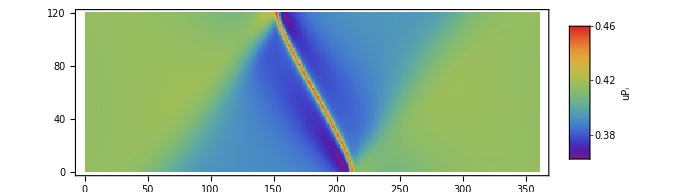

```mathematica
PP=Table[Subscript[P,3,x,1,z]-0.Subscript[P,3,x,1,z]+0.Subscript[u,2,x,2,z]+0.Subscript[u,2,x,2,z]-0.Subscript[u,2,x,1,z],{x,1,Lx+1},{z,1,Lz}]ᵀ/.res[[2]];
dispRange=MinMax@Flatten[PP]
Mean[Abs[PP//Flatten]]
ListDensityPlot[PP,AspectRatio->Lz/Lx,ImageSize->Large,ColorFunctionScaling->True,ColorFunction->"Rainbow",InterpolationOrder->0,PlotLegends->Placed[BarLegend[{"Rainbow",dispRange},LabelStyle->{Black,Bold,10},LegendLayout->"Column",LegendMargins->0,LegendLabel->Placed[Style["uP_i",20],Top]],Right],PlotRange->dispRange]
```

### phonons

```mathematica
DispatchRes=Dispatch[res[[2]]];
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}]
Timing[M=CoefficientArrays[fDisc,vars,"Symmetric"->False]]
```

SparseArrayOptions→{DotDensityThreshold→1.,DotDensityVectorThreshold→0.25,DotLengthThreshold→10,GraphicsFactor→0.075,IndexHashThreshold→0.01,SortDensityThreshold→0.1,SortLengthThreshold→10,TreatRepeatedEntries→Total}

{0.100498,{0.,SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}}

```mathematica
(M[[1]]+M[[2]].vars+M[[3]].vars.vars+M[[4]].vars.vars.vars+M[[5]].vars.vars.vars.vars//Expand)==fDisc
```

True

```mathematica
Timing[AR=ArrayRules[M[[3]]][[;;-2]];
M3=Sum[SparseArray[Table[{ele[[1]][[i[[1]]]],ele[[1]][[i[[2]]]]}->ele[[2]],{ele,AR}],{Length[vars],Length[vars]}],{i,Permutations[{1,2}]}]]
```

{0.041661,SparseArray[…]}

```mathematica
(*Timing[AR=ArrayRules[M[[3]]][[;;-2]];
M3Rules=Table[ele[[1]][[1]]->ele[[1]][[2]]ele[[2]],{ele,Tally[Flatten[Table[{ele[[1]][[i[[1]]]],ele[[1]][[i[[2]]]]}->ele[[2]],{ele,AR},{i,Permutations[{1,2}]}]]]}];
M3=SparseArray[M3Rules]]*)
```

```mathematica
Timing[AR=ArrayRules[M[[4]]][[;;-2]];
M4=Sum[SparseArray[Table[{ele[[1]][[i[[1]]]],ele[[1]][[i[[2]]]]}->ele[[2]]vars⟦ele[[1]]⟦i⟦3⟧⟧⟧,{ele,AR}]/.DispatchRes,{Length[vars],Length[vars]}],{i,Permutations[{1,2,3}]}]]
```

{1.51801,SparseArray[…]}

```mathematica
Timing[AR=ArrayRules[M[[5]]][[;;-2]];
M5=Sum[SparseArray[Table[{ele[[1]][[i[[1]]]],ele[[1]][[i[[2]]]]}->0.5ele[[2]] vars⟦ele[[1]]⟦i⟦3⟧⟧⟧vars⟦ele[[1]]⟦i⟦4⟧⟧⟧,{ele,AR}]/.DispatchRes,{Length[vars],Length[vars]}],{i,Permutations[{1,2,3,4}]}]]
```

{2.68322,SparseArray[…]}

```mathematica
Timing[Hmat=M3+M4+M5]
```

{0.000173,SparseArray[…]}

```mathematica
Timing[HessianRules=ArrayRules[Hmat]];
```

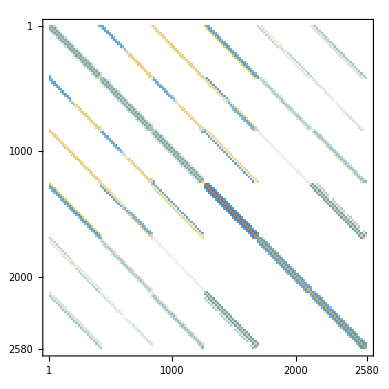

```mathematica
MatrixPlot[Hmat]
```

```mathematica
Export["tiltedM.dat",Join[#1-1,{#2}]&@@@(Sort@HessianRules)]
Export["vars.dat",vars]
```